## Qx this part is to compute Qx0 and Qx1

```mathematica
(*p=ⅇ^(β (J Cos[θ1-θ2]+μ (Cos[θ1]+Cos[θ2]) Ex))
Normal[Series[p,{Ex,0,3}]]*)
```

```mathematica
(*p0=Normal[Series[p,{Ex,0,0}]]
p1=Normal[Series[p,{Ex,0,1}]]-p0
p2=Normal[Series[p,{Ex,0,2}]]-p1-p0
p3=Normal[Series[p,{Ex,0,3}]]-p2-p1-p0*)
```

```mathematica
(*q0=Integrate[p0,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

```mathematica
(*4 π^2 BesselI[0,J β];*)
```

```mathematica
(*q1=Integrate[p1,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

```mathematica
(*q2=Integrate[p2,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

```mathematica
(*2 Ex^2 π^2 β^2 μ^2 (BesselI[0,J β]+BesselI[1,J β]);*)
```

```mathematica
(*q3=Integrate[p3,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

It seems odd terms are all zero.

```mathematica
(*q=q0+q1+q2+q3;
Normal[Series[1/q D[q,Ex],{Ex,0,3}]]*)
```

```mathematica
(*(Ex β^2 μ^2 (BesselI[0,J β]+BesselI[1,J β]))/BesselI[0,J β]-(Ex^3 β^4 μ^4 (BesselI[0,J β]+BesselI[1,J β])^2)/(2 BesselI[0,J β]^2);*)
```

So

```mathematica
(*Qx0=0;
Qx1=β^2 μ^2+(β^2 μ^2 BesselI[1,J β])/BesselI[0,J β];*)
```

## test for F(theta1,theta 2)

need to solve possion function

note bmu = β μ and bJ= β J

(∂^2 ψ)/(∂theta1^2)+(∂^2 ψ)/(∂theta2^2)=(-bmu(Cos[theta1]+Cos[theta2]+QX))Exp[bJ Cos[theta1-theta2]+bmu Ε (Cos[theta1]+Cos[theta2])];

```mathematica
Qx=Qx0+Qx1 Ε;
Qx0=0;
F[theta1_,theta2_]:=(-bmu(Cos[theta1]+Cos[theta2])+Qx)Exp[bJ Cos[theta1-theta2]+bmu Ε (Cos[theta1]+Cos[theta2])]
F0=Normal[Series[F[theta1,theta2],{Ε,0,0}]]//Simplify
F1=(Normal[Series[F[theta1,theta2],{Ε,0,1}]]-F0)//Simplify
```

-bmu ⅇ^(bJ Cos[theta1-theta2]) (Cos[theta1]+Cos[theta2])

ⅇ^(bJ Cos[theta1-theta2]) Ε (Qx1-bmu^2 Cos[theta1]^2-2 bmu^2 Cos[theta1] Cos[theta2]-bmu^2 Cos[theta2]^2)

```mathematica
Qy=Qy0+Qy1 Ε;
Qy0=0;
F[theta1_,theta2_]:=(-bmu(Sin[theta1]+Sin[theta2])+Qy)Exp[bJ Cos[theta1-theta2]+bmu Ε ( Sin[theta1]+Sin[theta2])]
F0=Normal[Series[F[theta1,theta2],{Ε,0,0}]]//Simplify
F1=(Normal[Series[F[theta1,theta2],{Ε,0,1}]]-F0)//Simplify
```

-bmu ⅇ^(bJ Cos[theta1-theta2]) (Sin[theta1]+Sin[theta2])

ⅇ^(bJ Cos[theta1-theta2]) Ε (Qy1-bmu^2 Sin[theta1]^2-2 bmu^2 Sin[theta1] Sin[theta2]-bmu^2 Sin[theta2]^2)

add one more expansion

```mathematica
Exp[bJ Cos[theta1-theta2]]=∑_(j=0)^N (bJ)^j/j! Cos[theta1-theta2]^j ;
```

Set::write: Tag Exp in Exp[bJ Cos[theta1-theta2]] is Protected.

then we have

## Set up

### Expressions

#### vE

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
Qx0=0;
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1-bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

IOcch means:∫_0^(2 π) H0c Cosh[2 Pi-xi]ⅆxi  0CCH etc.. and 0 means zero order of Ε

```mathematica
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

```mathematica
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
```

```mathematica
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
```

Note the 0 of  A0C(A_0(θ1))  here means zero order of Ε
A0c[0,j,theta1] here is A_0(θ_1) in steven’s sol, this part could be include in ∑_(n=1)^∞ A_n_c Cos(nθ2) so it could start with n=0 i.e. ∑_(n=0)^∞ A_n_c Cos(nθ2) since Cos(nθ2) = 1 for n = 0;

```mathematica
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
```

```mathematica
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
```

```mathematica
pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

```mathematica
(*pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]*)
```

#### vEE

```mathematica
H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

small question here, I1CCH integrate along theta1?

```mathematica
F1s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1sch[n,j,2Pi]+1/(2n)I1ssh[n,j,2Pi]
F1c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1cch[n,j,2Pi]+1/(2n)I1csh[n,j,2Pi]
E1s[n_,j_]:=F1s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1ssh[n,j,2Pi]
E1c[n_,j_]:=F1c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1csh[n,j,2Pi]
```

```mathematica
A1c[0,j_,theta1_]:=Integrate[H1[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A1s[0,j_,theta1_]:=0
A1s[n_,j_,theta1_]:=E1s[n,j]Sinh[n theta1]+F1s[n,j]Cosh[n theta1]+1/n I1ssh[n,j,theta1]
A1c[n_,j_,theta1_]:=E1c[n,j]Sinh[n theta1]+F1c[n,j]Cosh[n theta1]+1/n I1csh[n,j,theta1]
dA1c[0,j_,theta1_]:=Integrate[H1[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA1s[0,j_,theta1_]:=0
dA1s[n_,j_,theta1_]:=n E1s[n,j]Cosh[n theta1]+n F1s[n,j]Sinh[n theta1]+I1sch[n,j,theta1]
dA1c[n_,j_,theta1_]:=n E1c[n,j]Cosh[n theta1]+n F1c[n,j]Sinh[n theta1]+I1cch[n,j,theta1]
```

```mathematica
pv11[bJx_,bmux_,theta1_,theta2_]:=Sum[dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux},{n,0,nmax},{j,0,jmax}]
pv21[bJx_,bmux_,theta1_,theta2_]:=Sum[n A1s[n,j,theta1]Cos[n theta2]-n A1c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]
```

### Export and import zero order

#### H0ns

```mathematica
(*Flatten[Table[{n,j,H0[0,j,t1_]:=Release[H0[0,j,t1]]},{j,0,10}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0x.xls",Table[{j,H0[0,j,theta1]},{j,0,10}]];*)
```

Fully Check for H0

```mathematica
H0x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0x.xls"],1];
```

```mathematica
c2=RandomInteger[{0,10}]
H0[0,c2,theta1]-ToExpression[H0x[[c2+1,2]]]
```

```mathematica
Table[H0[0,j_,xi_]:=ToExpression[H0x[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,H0c[n,j,t1_]:=Release[H0c[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0cx.xls",Table[{n,j,H0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
H0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{5,10}];
H0c[c1,c2,theta1]
test=H0c[c1,c2,theta1]-ToExpression[H0cx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2,",",test]*)
```

```mathematica
Table[H0c[n_,j_,xi_]:=ToExpression[H0cx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,H0s[n,j,t1_]:=Release[H0s[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0sx.xls",Table[{n,j,H0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

Checked for H0s

```mathematica
H0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{5,10}];
H0s[c1,c2,theta1]
test=H0s[c1,c2,theta1]-ToExpression[H0sx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2,",",test]*)
```

```mathematica
Table[H0s[n_,j_,xi_]:=ToExpression[H0sx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### I0cch

```mathematica
(*Flatten[Table[{n,j,I0cch[n,j,t1_]:=Release[I0cch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Timing[Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cchx.xls",Table[{n,j,I0cch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify]];*)
```

```mathematica
I0cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cchx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{5,10}];
test=I0cch[c1,c2,theta1]-ToExpression[I0cchx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2,",  ", test]*)
```

```mathematica
Table[I0cch[n_,j_,xi_]:=ToExpression[I0cchx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{1,10}];
Print[c1," , " , c2 ," , ", I0cchx[[11*(c1-1)+c2+1,1]]," , " ,I0cchx[[11*(c1-1)+c2+1,2]]]*)
```

```mathematica
(*Flatten[Table[{n,j,I0sch[n,j,t1_]:=Release[I0sch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0schx.xls",Table[{n,j,I0sch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I0schx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0schx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{4,5}];
I0sch[c1,c2,theta1];
test=I0sch[c1,c2,theta1]-ToExpression[I0schx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2,"," ,test]*)
```

```mathematica
Table[I0sch[n_,j_,xi_]:=ToExpression[I0schx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,I0csh[n,j,t1_]:=Release[I0csh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cshx.xls",Table[{n,j,I0csh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I0cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
I0csh[c1,c2,theta1]
test=I0csh[c1,c2,theta1]-ToExpression[I0cshx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2," ,", test]
*)
```

```mathematica
Table[I0csh[n_,j_,xi_]:=ToExpression[I0cshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,I0ssh[n,j,t1_]:=Release[I0ssh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0sshx.xls",Table[{n,j,I0ssh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I0sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0sshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
I0ssh[c1,c2,theta1]
test=I0ssh[c1,c2,theta1]-ToExpression[I0sshx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2," ,", test]*)
```

```mathematica
Table[I0ssh[n_,j_,xi_]:=ToExpression[I0sshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### F0ns

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0sx.xls",Table[{n,j,F0s[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
F0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
F0s[c1,c2];//Simplify
test=Simplify[F0s[c1,c2]]-ToExpression[F0sx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2," ,", test]*)
```

```mathematica
Table[F0s[n_,j_]:=ToExpression[F0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*

Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0cx.xls",Table[{n,j,F0c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
F0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
F0c[c1,c2];//Simplify
test=Simplify[F0c[c1,c2]]-ToExpression[F0cx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2," ,", test]//FullSimplify*)
```

```mathematica
Table[F0c[n_,j_]:=ToExpression[F0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### E0ns

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0sx.xls",Table[{n,j,E0s[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
E0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
E0s[c1,c2]//Simplify
test=Simplify[E0s[c1,c2]]-ToExpression[E0sx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2," ,", test]//FullSimplify*)
```

```mathematica
Table[E0s[n_,j_]:=ToExpression[E0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0cx.xls",Table[{n,j,E0c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
E0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
E0c[c1,c2]//Simplify
test=Simplify[E0c[c1,c2]]-ToExpression[E0cx[[11*(c1-1)+c2+1,3]]];
Print[c1,",",c2," ,", test]//FullSimplify*)
```

```mathematica
Table[E0c[n_,j_]:=ToExpression[E0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### test

```mathematica
(*Flatten[Table[{n,j,A0c[n,j,theta1_]:=Release[A0c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];*)
```

```mathematica
(*Flatten[Table[{n,j,dA0c[0,j,theta1_]:=Release[dA0c[0,j,theta1]]},{j,0,10}]//Simplify,1];*)
```

#### A0n and dA0n

```mathematica
(*Flatten[Table[{n,j,A0c[n,j,theta1_]:=Release[A0c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx0.xls",Table[{n,j,A0c[0,j,theta1]},{n,0,0},{j,0,10}]//Simplify];
Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx.xls",Table[{n,j,A0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
A0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx0.xls"],1];
A0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx.xls"],1];
```

```mathematica
(*For[i=0,i<1,i++,
c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
A1=A0c[c1,c2,theta1];
A2=ToExpression[A0cx[[11*(c1-1)+c2+1,3]]];
test=A1-A2//Simplify;
Print[c1,",",c2," ,", test];
]*)
```

```mathematica
(*c2=RandomInteger[{0,10}]
A0c[0,c2,theta1]
A0c[0,c2,theta1]-ToExpression[A0cx0[[c2+1,3]]]//Simplify*)
```

```mathematica
Table[A0c[0,j_,theta1_]:=ToExpression[A0cx0[[j+1,3]]],{j,0,10}];
Table[A0c[n_,j_,theta1_]:=ToExpression[A0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,A0s[n,j,theta1_]:=Release[A0s[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0sx.xls",Table[{n,j,A0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
A0sx=Flatten[Import["/home/weisongl/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0sx.xls"],1];
```

```mathematica
(*For[i=0,i<2,i++,
c1=RandomInteger[{1,5}];
c2=RandomInteger[{3,5}];
A1=A0s[c1,c2,theta1];
A2=ToExpression[A0sx[[11*(c1-1)+c2+1,3]]];
test=A1-A2//Simplify;
Print[c1,",",c2," ,", test]
]*)
```

```mathematica
A0s[0,j,theta1]:=0;
Table[A0s[n_,j_,theta1_]:=ToExpression[A0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,dA0c[0,j,theta1_]:=Release[dA0c[0,j,theta1]]},{n,0,5}，{j,0,10}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx.xls",Table[{n,j,dA0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx0.xls",Table[{n,j,dA0c[0,j,theta1]},{n,0,0},{j,0,10}]//Simplify];*)
```

```mathematica
dA0c[0,1,theta1]
```

-1/2 bJ bmu Sin[theta1]

```mathematica
dA0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx0.xls"],1];
dA0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx.xls"],1];
```

```mathematica
(*For[i=0,i<2,i++,
c1=RandomInteger[{1,5}];
c2=RandomInteger[{5,10}];
A1=dA0c[c1,c2,theta1];
A2=ToExpression[dA0cx[[11*(c1-1)+c2+1,3]]];
test=A1-A2//Simplify;
Print[c1,",",c2," ,", test];
]*)
```

```mathematica
(*c2=RandomInteger[{5,10}]
dA0c[0,c2,theta1]
dA0c[0,c2,theta1]-ToExpression[dA0cx0[[c2+1,3]]]*)
```

```mathematica
Table[dA0c[0,j_,theta1_]:=ToExpression[dA0cx0[[j+1,3]]],{j,0,10}];
Table[dA0c[n_,j_,theta1_]:=ToExpression[dA0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,dA0s[0,j,theta1_]:=Release[dA0s[0,j,theta1]]},{n,0,5}，{j,0,10}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0sx.xls",Table[{n,j,dA0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
dA0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0sx.xls"],1];
```

```mathematica
(*For[i=0,i<2,i++,
c1=RandomInteger[{1,5}];
c2=RandomInteger[{5,10}];
A1=dA0s[c1,c2,theta1];
A2=ToExpression[dA0sx[[11*(c1-1)+c2+1,3]]];
test=A1-A2//Simplify;
Print[c1,",",c2," ,", test];
]*)
```

```mathematica
dA0s[0,j,theta1]:=0;
Table[dA0s[n_,j_,theta1_]:=ToExpression[dA0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

### Export and import first order

#### H1ns

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1x.xls",Table[{j,H1[0,j,theta1]},{j,0,10}]//Simplify];*)
H1x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1x.xls"],1];
```

```mathematica
(*c2=RandomInteger[{5,10}];H1[0,c2,theta1]-ToExpression[H1x[[c2+1,2]]]//Simplify*)
```

```mathematica
Table[H1[0,j_,xi_]:=ToExpression[H1x[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1cx.xls",Table[{n,j,H1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
H1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];c2=RandomInteger[{8,10}];
H1c[c1,c2,theta1]-ToExpression[H1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1c[n_,j_,xi_]:=ToExpression[H1cx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1sx.xls",Table[{n,j,H1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
H1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];c2=RandomInteger[{8,10}];
H1s[c1,c2,theta1]//Simplify
H1s[c1,c2,theta1]-ToExpression[H1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1s[n_,j_,xi_]:=ToExpression[H1sx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### I1ns

```mathematica
(*Flatten[Table[{n,j,I1cch[n,j,t1_]:=Release[I1cch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Timing[Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cchx.xls",Table[{n,j,I1cch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify]]*)
```

```mathematica
I1cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cchx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1cch[c1,c2,theta1]-ToExpression[I1cchx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1cch[n_,j_,xi_]:=ToExpression[I1cchx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,I1sch[n,j,t1_]:=Release[I1sch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1schx.xls",Table[{n,j,I1sch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I1schx=Flatten[Import["/home/weisongl/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sch.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1sch[c1,c2,theta1]-ToExpression[I1schx[[11*(c1-1)+c2+1,3]]]*)
```

```mathematica
Table[I1sch[n_,j_,xi_]:=ToExpression[I1schx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,I1csh[n,j,t1_]:=Release[I1csh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cshx.xls",Table[{n,j,I1csh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I1cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1csh[c1,c2,theta1]-ToExpression[I1cshx[[11*(c1-1)+c2+1,3]]]*)
```

```mathematica
Table[I1csh[n_,j_,xi_]:=ToExpression[I1cshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,I1ssh[n,j,t1_]:=Release[I1ssh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sshx.xls",Table[{n,j,I1ssh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I1sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1ssh[c1,c2,theta1]-ToExpression[I1sshx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1ssh[n_,j_,xi_]:=ToExpression[I1sshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### Ans

```mathematica
(*Flatten[Table[{n,j,A1c[n,j,theta1_]:=Release[A1c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1cx.xls",Table[{n,j,A1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
A1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
A1c[c1,c2,theta1]-ToExpression[A1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1c[n_,j_,theta1_]:=ToExpression[A1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,A1s[n,j,theta1_]:=Release[A1s[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1sx.xls",Table[{n,j,A1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
A1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{0,5}];
A1s[c1,c2,theta1]-ToExpression[A1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1s[n_,j_,theta1_]:=ToExpression[A1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,dA1c[0,j,theta1_]:=Release[dA1c[0,j,theta1]]},{n,0,5},{j,0,10}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1cx.xls",Table[{n,j,dA1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
dA1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1c[c1,c2,theta1]-ToExpression[dA1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1c[n_,j_,theta1_]:=ToExpression[dA1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Flatten[Table[{n,j,dA1c[0,j,theta1_]:=Release[dA1c[0,j,theta1]]},{n,0,5},{j,0,10}]//Simplify,1];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1sx.xls",Table[{n,j,dA1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
dA1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1s[c1,c2,theta1]-ToExpression[dA1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1s[n_,j_,theta1_]:=ToExpression[dA1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

## Pv10 and pv20

```mathematica
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

Part::pkspec1: The expression 1+j+11 (-1+n) cannot be used as a part specification.

ToExpression::notstrbox: {{1.,0.,0.},{1.,1.,(bJ*bmu*Cos[2*theta1])/5},{1.,2.,(bJ^2*bmu*Cos[2*theta1])/20},{1.,3.,(bJ^3*bmu*Cos[2*theta1])/40},{1.,4.,(bJ^4*bmu*Cos[2*theta1])/240},{1.,5.,(bJ^5*bmu*Cos[2*theta1])/960},{1.,6.,(bJ^6*bmu*Cos[2*theta1])/7680},«37»,{5.,0.,0.},{5.,1.,0.},{5.,2.,0.},{5.,3.,0.},{5.,4.,(bJ^4*bmu*Cos[4*theta1])/3936},{5.,5.,(bJ^5*bmu*(122*Cos[4*theta1] + 123*Cos[6*theta1]))/4801920},«5»}⟦1+j+11 (-1+n),3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::pkspec1: The expression 1+j+11 (-1+n) cannot be used as a part specification.

ToExpression::notstrbox: {{1.,0.,0.},{1.,1.,(-2*bJ*bmu*Cos[theta1]*Sin[theta1])/5},{1.,2.,-(bJ^2*bmu*Cos[theta1]*Sin[theta1])/10},{1.,3.,-(bJ^3*bmu*Cos[theta1]*Sin[theta1])/20},{1.,4.,-(bJ^4*bmu*Cos[theta1]*Sin[theta1])/120},{1.,5.,-(bJ^5*bmu*Cos[theta1]*Sin[theta1])/480},{1.,6.,-(bJ^6*bmu*Cos[theta1]*Sin[theta1])/3840},«37»,{5.,0.,0.},{5.,1.,0.},{5.,2.,0.},{5.,3.,0.},{5.,4.,-(bJ^4*bmu*Sin[4*theta1])/3936},{5.,5.,-(bJ^5*bmu*(122*Sin[4*theta1] + 123*Sin[6*theta1]))/4801920},«5»}⟦«1»,3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

∑_(n=0)^nmax ∑_(j=0)^jmax ($Failed Cos[n theta2]+$Failed Sin[n theta2])

Part::pkspec1: The expression 1+j+11 (-1+n) cannot be used as a part specification.

ToExpression::notstrbox: {{1.,0.,0.},{1.,1.,(bJ*bmu*Cos[theta1]*Sin[theta1])/5},{1.,2.,(bJ^2*bmu*Sin[2*theta1])/40},{1.,3.,(bJ^3*bmu*Sin[2*theta1])/80},{1.,4.,(bJ^4*bmu*Sin[2*theta1])/480},{1.,5.,(bJ^5*bmu*Cos[theta1]*Sin[theta1])/960},{1.,6.,(bJ^6*bmu*Cos[theta1]*Sin[theta1])/7680},{1.,7.,(bJ^7*bmu*Sin[2*theta1])/92160},«36»,{5.,0.,0.},{5.,1.,0.},{5.,2.,0.},{5.,3.,0.},{5.,4.,(bJ^4*bmu*Sin[4*theta1])/15744},{5.,5.,(bJ^5*bmu*(61*Sin[4*theta1] + 41*Sin[6*theta1]))/9603840},«5»}⟦«1»⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::pkspec1: The expression 1+j+11 (-1+n) cannot be used as a part specification.

ToExpression::notstrbox: {{1.,0.,0. + bmu},{1.,1.,(bJ*bmu*(5 + Cos[2*theta1]))/10},{1.,2.,(bJ^2*bmu*(10 + Cos[2*theta1]))/40},{1.,3.,(bJ^3*bmu*(5 + Cos[2*theta1]))/80},{1.,4.,(bJ^4*bmu*(15 + 2*Cos[2*theta1]))/960},{1.,5.,(bJ^5*bmu*(5 + Cos[2*theta1]))/1920},{1.,6.,(bJ^6*bmu*(20 + 3*Cos[2*theta1]))/46080},«37»,{5.,0.,0.},{5.,1.,0.},{5.,2.,0.},{5.,3.,0.},{5.,4.,(bJ^4*bmu*Cos[4*theta1])/15744},{5.,5.,(bJ^5*bmu*(61*Cos[4*theta1] + 41*Cos[6*theta1]))/9603840},«5»}⟦1+j+11 (-1+n),3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

∑_(n=1)^nmax ∑_(j=0)^jmax (n $Failed Cos[n theta1]-n $Failed Sin[n theta1])

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

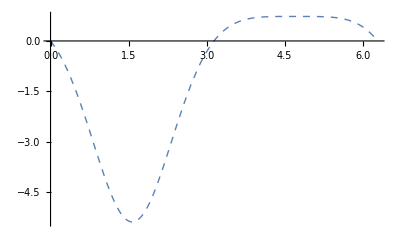

```mathematica
nmax=jmax=4;
myt2=Pi/2;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

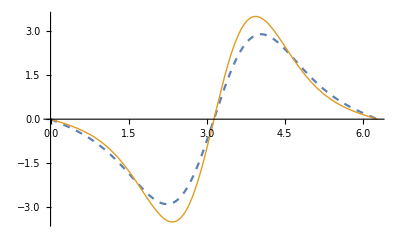

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
pv10[1,1,theta1,theta2]
```

0.-(117 Sin[theta1])/64+(0.+1/240 (Cos[2 theta1]-Cosh[theta1])+Cosh[theta1]/240) Sin[theta2]+(0.+1/40 (Cos[2 theta1]-Cosh[theta1])+Cosh[theta1]/40) Sin[theta2]+(0.+1/20 (Cos[2 theta1]-Cosh[theta1])+Cosh[theta1]/20) Sin[theta2]+(0.+1/5 (Cos[2 theta1]-Cosh[theta1])+Cosh[theta1]/5) Sin[theta2]+(0.+(13 Cos[theta1]+15 Cos[3 theta1]-28 Cosh[2 theta1])/6240+(7 Cosh[2 theta1])/1560) Sin[2 theta2]+(0.+(13 Cos[theta1]+5 Cos[3 theta1]-18 Cosh[2 theta1])/1040+9/520 Cosh[2 theta1]) Sin[2 theta2]+(0.+1/520 (13 Cos[theta1]+15 Cos[3 theta1]-28 Cosh[2 theta1])+7/130 Cosh[2 theta1]) Sin[2 theta2]+(0.+1/10 (Cos[theta1]-Cosh[2 theta1])+1/10 Cosh[2 theta1]) Sin[2 theta2]+(0.+(50 Cos[2 theta1]+13 Cos[4 theta1]-63 Cosh[3 theta1])/31200+(21 Cosh[3 theta1])/10400) Sin[3 theta2]+(0.+(25 Cos[2 theta1]+26 Cos[4 theta1]-51 Cosh[3 theta1])/7800+(17 Cosh[3 theta1])/2600) Sin[3 theta2]+(0.+1/52 (Cos[2 theta1]-Cosh[3 theta1])+1/52 Cosh[3 theta1]) Sin[3 theta2]+(0.+(123 Cos[3 theta1]+125 Cos[5 theta1]-248 Cosh[4 theta1])/393600+(31 Cosh[4 theta1])/49200) Sin[4 theta2]+(0.+1/400 (Cos[3 theta1]-Cosh[4 theta1])+1/400 Cosh[4 theta1]) Sin[4 theta2]+Cos[theta2] (0.+1/960 (-4 Sin[2 theta1]-17 Sinh[theta1])+(17 Sinh[theta1])/960)+Cos[theta2] (0.+1/40 (-Sin[2 theta1]-3 Sinh[theta1])+(3 Sinh[theta1])/40)+Cos[theta2] (0.+1/40 (-2 Sin[2 theta1]-11 Sinh[theta1])+(11 Sinh[theta1])/40)+Cos[theta2] (0.+1/5 (-Sin[2 theta1]-3 Sinh[theta1])+(3 Sinh[theta1])/5)+Cos[2 theta2] (0.+(-13 Sin[theta1]-15 Sin[3 theta1]-36 Sinh[2 theta1])/6240+3/520 Sinh[2 theta1])+Cos[2 theta2] (0.+(-39 Sin[theta1]-15 Sin[3 theta1]-88 Sinh[2 theta1])/3120+11/390 Sinh[2 theta1])+Cos[2 theta2] (0.+1/520 (-13 Sin[theta1]-15 Sin[3 theta1]-36 Sinh[2 theta1])+9/130 Sinh[2 theta1])+Cos[2 theta2] (0.+1/10 (-Sin[theta1]-2 Sinh[2 theta1])+1/5 Sinh[2 theta1])+Cos[3 theta2] (0.+(-200 Sin[2 theta1]-52 Sin[4 theta1]-339 Sinh[3 theta1])/124800+(113 Sinh[3 theta1])/41600)+Cos[3 theta2] (0.+(-25 Sin[2 theta1]-26 Sin[4 theta1]-57 Sinh[3 theta1])/7800+(19 Sinh[3 theta1])/2600)+Cos[3 theta2] (0.+1/104 (-2 Sin[2 theta1]-3 Sinh[3 theta1])+3/104 Sinh[3 theta1])+Cos[4 theta2] (0.+(-123 Sin[3 theta1]-125 Sin[5 theta1]-264 Sinh[4 theta1])/393600+(11 Sinh[4 theta1])/16400)+Cos[4 theta2] (0.+(-3 Sin[3 theta1]-4 Sinh[4 theta1])/1200+1/300 Sinh[4 theta1])

$Aborted

$Aborted

$Aborted

Show::gcomb: Could not combine the graphics objects in ….

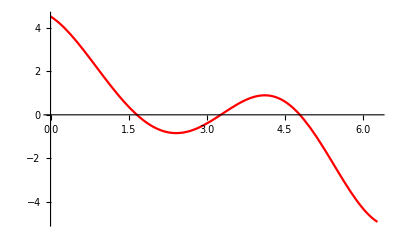
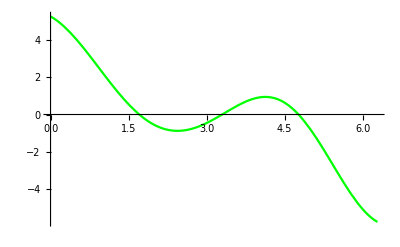
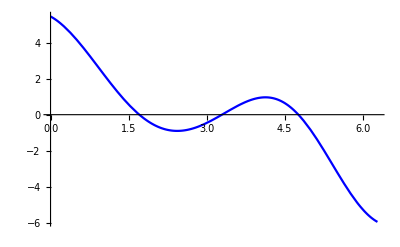
Show[{-Graphics-,-Graphics-,-Graphics-,plot[4],plot[5],plot[6]},PlotRange→All,PlotLabel→θ2 = 3π/2]

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=2;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=3;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=4;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=5;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
plot[nmax+1]=Plot[pv20[1,1,myt2,theta2],{theta2,0,2Pi},PlotStyle->{Dashed,Thick}];
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```

### output

```mathematica
Qx1=bmu^2;(*for coupling J is zero*)
Qx1=bmu^2+(bmu^2  BesselI[1,bJ])/BesselI[0,bJ]/.{bmu->1,bJ->1}//N
```

1.44639

```mathematica
colors={Red,Green,Blue,Orange,Black};
```

```mathematica
nmax=1;jmax=10;
myt2=Pi;
(*Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]*)
```

```mathematica
nmax=3;jmax=10;
myt2=Pi;
(*Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]*)
```

```mathematica
nmax=5;jmax=10;
myt2=Pi;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

$Aborted

```mathematica
nmax=jmax=4;
myt2=Pi/2;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

$Aborted

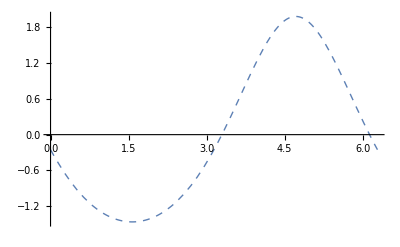

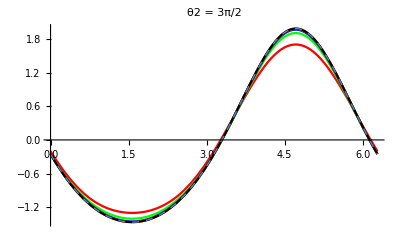

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=2;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=3;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=4;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=5;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
plot[nmax+1]=Plot[pv20[1,1,myt2,theta2],{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```

```mathematica
nmax= jmax=1;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

-(3 Sin[theta1])/2-1/5 Sin[2 theta1-theta2]

(-1.5-0.1 Cos[2 theta2]) Sin[theta1]+0.2 Cos[theta1] Cos[theta2] Sin[theta2]

```mathematica
nmax= jmax=3;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

1/15600(-28275 Sin[theta1]-350 Sin[2 theta1-3 theta2]-52 Sin[4 theta1-3 theta2]-2145 Sin[theta1-2 theta2]-525 Sin[3 theta1-2 theta2]-4290 Sin[2 theta1-theta2])

-1.8125 Sin[theta1]-0.0025 Sin[3 theta1-4 theta2]-0.0224359 Sin[2 theta1-3 theta2]-0.1375 Sin[theta1-2 theta2]-0.0336538 Sin[3 theta1-2 theta2]-0.275 Sin[2 theta1-theta2]

```mathematica
nmax= jmax=5;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

-(703 Sin[theta1])/384-(11 Sin[4 theta1-5 theta2])/39360-Sin[6 theta1-5 theta2]/39040-(19 Sin[3 theta1-4 theta2])/6400-(11 Sin[5 theta1-4 theta2])/31488-(121 Sin[2 theta1-3 theta2])/4992-(19 Sin[4 theta1-3 theta2])/4800-(269 Sin[theta1-2 theta2])/1920-(121 Sin[3 theta1-2 theta2])/3328-269/960 Sin[2 theta1-theta2]

-1.83073 Sin[theta1]-0.0000213456 Sin[5 theta1-6 theta2]-0.000279472 Sin[4 theta1-5 theta2]-0.00296875 Sin[3 theta1-4 theta2]-0.000349339 Sin[5 theta1-4 theta2]-0.0242388 Sin[2 theta1-3 theta2]-0.00395833 Sin[4 theta1-3 theta2]-0.140104 Sin[theta1-2 theta2]-0.0363582 Sin[3 theta1-2 theta2]-0.280208 Sin[2 theta1-theta2]

```mathematica
nmax=5; jmax=10;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

(-184365854430030 Sin[theta1]-29551303600 Sin[4 theta1-5 theta2]-2910939525 Sin[6 theta1-5 theta2]-300895720164 Sin[3 theta1-4 theta2]-36939129500 Sin[5 theta1-4 theta2]-2445973873350 Sin[2 theta1-3 theta2]-401194293552 Sin[4 theta1-3 theta2]-14113315056295 Sin[theta1-2 theta2]-3668960810025 Sin[3 theta1-2 theta2]-28226630112590 Sin[2 theta1-theta2])/100678975488000

-1.83122 Sin[theta1]-0.0000240942 Sin[5 theta1-6 theta2]-0.00029352 Sin[4 theta1-5 theta2]-0.00298866 Sin[3 theta1-4 theta2]-0.0003669 Sin[5 theta1-4 theta2]-0.0242948 Sin[2 theta1-3 theta2]-0.00398489 Sin[4 theta1-3 theta2]-0.140181 Sin[theta1-2 theta2]-0.0364422 Sin[3 theta1-2 theta2]-0.280363 Sin[2 theta1-theta2]

```mathematica
Exp[bJ*Cos[theta2-theta1]];
```

## V^EE (E in first order)

### set up

what is A1 here???

```mathematica
(*A1[0,j_,theta1_]:=uld not contains theta1,uld not contains theta1,so there must be some mistakes here.so there must be some mistakes here.Integrate[h1[0,j](theta1-t1),{t1,0,theta1}]
A1[n_,j_,theta1_]:=2/n Integrate[h1[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h1[n,aj]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA1[0,j_,theta1_]:=Integrate[h1[0,j],{t1,0,theta1}]
dA1[n_,j_,theta1_]:=Integrate[h1[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-2Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]*)
```

## out put

```mathematica
Qx1=bmu^2+(bmu^2  BesselI[1,J β])/BesselI[0,J β];
Qx1=bmu^2;
```

```mathematica
pv11[bJ,bmu,theta1,theta2]//Simplify
pv21[bJ,bmu,theta1,theta2]//Simplify
```

-((bmu^2 (-60769684684800 bJ π-7596210585600 bJ^3 π-316508774400 bJ^5 π-6593932800 bJ^7 π-82424160 bJ^9 π+60769684684800 bJ theta1+7596210585600 bJ^3 theta1+316508774400 bJ^5 theta1+6593932800 bJ^7 theta1+82424160 bJ^9 theta1+343434 (88473600+88473600 bJ+33177600 bJ^2+11059200 bJ^3+2304000 bJ^4+460800 bJ^5+67200 bJ^6+9600 bJ^7+1080 bJ^8+120 bJ^9+11 bJ^10) Sin[2 theta1]+346320 bJ^3 (322560+80640 bJ+24192 bJ^2+4032 bJ^3+672 bJ^4+84 bJ^5+10 bJ^6+bJ^7) Sin[3 theta1-5 theta2]+1497000960 bJ^5 Sin[7 theta1-5 theta2]+249500160 bJ^6 Sin[7 theta1-5 theta2]+71285760 bJ^7 Sin[7 theta1-5 theta2]+8910720 bJ^8 Sin[7 theta1-5 theta2]+1392300 bJ^9 Sin[7 theta1-5 theta2]+139230 bJ^10 Sin[7 theta1-5 theta2]+18260121600 bJ^4 Sin[6 theta1-4 theta2]+3652024320 bJ^5 Sin[6 theta1-4 theta2]+1065173760 bJ^6 Sin[6 theta1-4 theta2]+152167680 bJ^7 Sin[6 theta1-4 theta2]+24455520 bJ^8 Sin[6 theta1-4 theta2]+2717280 bJ^9 Sin[6 theta1-4 theta2]+311355 bJ^10 Sin[6 theta1-4 theta2]+3038484234240 bJ Sin[theta1-3 theta2]+1519242117120 bJ^2 Sin[theta1-3 theta2]+506414039040 bJ^3 Sin[theta1-3 theta2]+126603509760 bJ^4 Sin[theta1-3 theta2]+23738158080 bJ^5 Sin[theta1-3 theta2]+3956359680 bJ^6 Sin[theta1-3 theta2]+527514624 bJ^7 Sin[theta1-3 theta2]+65939328 bJ^8 Sin[theta1-3 theta2]+6868680 bJ^9 Sin[theta1-3 theta2]+686868 bJ^10 Sin[theta1-3 theta2]+186181632000 bJ^3 Sin[5 theta1-3 theta2]+46545408000 bJ^4 Sin[5 theta1-3 theta2]+13963622400 bJ^5 Sin[5 theta1-3 theta2]+2327270400 bJ^6 Sin[5 theta1-3 theta2]+387878400 bJ^7 Sin[5 theta1-3 theta2]+48484800 bJ^8 Sin[5 theta1-3 theta2]+5772000 bJ^9 Sin[5 theta1-3 theta2]+577200 bJ^10 Sin[5 theta1-3 theta2]+759621058560 bJ^2 Sin[2 (theta1-2 theta2)]+253207019520 bJ^3 Sin[2 (theta1-2 theta2)]+79127193600 bJ^4 Sin[2 (theta1-2 theta2)]+15825438720 bJ^5 Sin[2 (theta1-2 theta2)]+2769451776 bJ^6 Sin[2 (theta1-2 theta2)]+395635968 bJ^7 Sin[2 (theta1-2 theta2)]+49454496 bJ^8 Sin[2 (theta1-2 theta2)]+5494944 bJ^9 Sin[2 (theta1-2 theta2)]+539682 bJ^10 Sin[2 (theta1-2 theta2)]+1519242117120 bJ^2 Sin[4 theta1-2 theta2]+506414039040 bJ^3 Sin[4 theta1-2 theta2]+158254387200 bJ^4 Sin[4 theta1-2 theta2]+31650877440 bJ^5 Sin[4 theta1-2 theta2]+5538903552 bJ^6 Sin[4 theta1-2 theta2]+791271936 bJ^7 Sin[4 theta1-2 theta2]+98908992 bJ^8 Sin[4 theta1-2 theta2]+10989888 bJ^9 Sin[4 theta1-2 theta2]+1079364 bJ^10 Sin[4 theta1-2 theta2]+60769684684800 Sin[theta1-theta2]+22788631756800 bJ^2 Sin[theta1-theta2]+1582543872000 bJ^4 Sin[theta1-theta2]+46157529600 bJ^6 Sin[theta1-theta2]+741817440 bJ^8 Sin[theta1-theta2]+7555548 bJ^10 Sin[theta1-theta2]+15192421171200 bJ Sin[2 (theta1-theta2)]+2532070195200 bJ^3 Sin[2 (theta1-theta2)]+118690790400 bJ^5 Sin[2 (theta1-theta2)]+2637573120 bJ^7 Sin[2 (theta1-theta2)]+34343400 bJ^9 Sin[2 (theta1-theta2)]+2532070195200 bJ^2 Sin[3 (theta1-theta2)]+263757312000 bJ^4 Sin[3 (theta1-theta2)]+9231505920 bJ^6 Sin[3 (theta1-theta2)]+164848320 bJ^8 Sin[3 (theta1-theta2)]+1798940 bJ^10 Sin[3 (theta1-theta2)]+316508774400 bJ^3 Sin[4 (theta1-theta2)]+23738158080 bJ^5 Sin[4 (theta1-theta2)]+659393280 bJ^7 Sin[4 (theta1-theta2)]+9812400 bJ^9 Sin[4 (theta1-theta2)]+31650877440 bJ^4 Sin[5 (theta1-theta2)]+1846301184 bJ^6 Sin[5 (theta1-theta2)]+42389568 bJ^8 Sin[5 (theta1-theta2)]+539682 bJ^10 Sin[5 (theta1-theta2)]+9115452702720 bJ Sin[3 theta1-theta2]+4557726351360 bJ^2 Sin[3 theta1-theta2]+1519242117120 bJ^3 Sin[3 theta1-theta2]+379810529280 bJ^4 Sin[3 theta1-theta2]+71214474240 bJ^5 Sin[3 theta1-theta2]+11869079040 bJ^6 Sin[3 theta1-theta2]+1582543872 bJ^7 Sin[3 theta1-theta2]+197817984 bJ^8 Sin[3 theta1-theta2]+20606040 bJ^9 Sin[3 theta1-theta2]+2060604 bJ^10 Sin[3 theta1-theta2]+60769684684800 Sin[theta1+theta2]+30384842342400 bJ Sin[theta1+theta2]+15192421171200 bJ^2 Sin[theta1+theta2]+3798105292800 bJ^3 Sin[theta1+theta2]+949526323200 bJ^4 Sin[theta1+theta2]+158254387200 bJ^5 Sin[theta1+theta2]+26375731200 bJ^6 Sin[theta1+theta2]+3296966400 bJ^7 Sin[theta1+theta2]+412120800 bJ^8 Sin[theta1+theta2]+41212080 bJ^9 Sin[theta1+theta2]+4121208 bJ^10 Sin[theta1+theta2]))/121539369369600)

(bmu^2 (288600 bJ^3 (322560+80640 bJ+24192 bJ^2+4032 bJ^3+672 bJ^4+84 bJ^5+10 bJ^6+bJ^7) Sin[3 theta1-5 theta2]+49725 bJ^5 (10752+1792 bJ+512 bJ^2+64 bJ^3+10 bJ^4+bJ^5) Sin[7 theta1-5 theta2]+37 (255 bJ^4 (645120+129024 bJ+37632 bJ^2+5376 bJ^3+864 bJ^4+96 bJ^5+11 bJ^6) Sin[6 theta1-4 theta2]+13 (2142 bJ (4423680+2211840 bJ+737280 bJ^2+184320 bJ^3+34560 bJ^4+5760 bJ^5+768 bJ^6+96 bJ^7+10 bJ^8+bJ^9) Sin[theta1-3 theta2]+360 bJ^3 (322560+80640 bJ+24192 bJ^2+4032 bJ^3+672 bJ^4+84 bJ^5+10 bJ^6+bJ^7) Sin[5 theta1-3 theta2]+17 (6 bJ^2 (15482880+5160960 bJ+1612800 bJ^2+322560 bJ^3+56448 bJ^4+8064 bJ^5+1008 bJ^6+112 bJ^7+11 bJ^8) Sin[2 (theta1-2 theta2)]+3 bJ^2 (15482880+5160960 bJ+1612800 bJ^2+322560 bJ^3+56448 bJ^4+8064 bJ^5+1008 bJ^6+112 bJ^7+11 bJ^8) Sin[4 theta1-2 theta2]+3715891200 Sin[theta1-theta2]+1393459200 bJ^2 Sin[theta1-theta2]+96768000 bJ^4 Sin[theta1-theta2]+2822400 bJ^6 Sin[theta1-theta2]+45360 bJ^8 Sin[theta1-theta2]+462 bJ^10 Sin[theta1-theta2]+928972800 bJ Sin[2 (theta1-theta2)]+154828800 bJ^3 Sin[2 (theta1-theta2)]+7257600 bJ^5 Sin[2 (theta1-theta2)]+161280 bJ^7 Sin[2 (theta1-theta2)]+2100 bJ^9 Sin[2 (theta1-theta2)]+154828800 bJ^2 Sin[3 (theta1-theta2)]+16128000 bJ^4 Sin[3 (theta1-theta2)]+564480 bJ^6 Sin[3 (theta1-theta2)]+10080 bJ^8 Sin[3 (theta1-theta2)]+110 bJ^10 Sin[3 (theta1-theta2)]+19353600 bJ^3 Sin[4 (theta1-theta2)]+1451520 bJ^5 Sin[4 (theta1-theta2)]+40320 bJ^7 Sin[4 (theta1-theta2)]+600 bJ^9 Sin[4 (theta1-theta2)]+1935360 bJ^4 Sin[5 (theta1-theta2)]+112896 bJ^6 Sin[5 (theta1-theta2)]+2592 bJ^8 Sin[5 (theta1-theta2)]+33 bJ^10 Sin[5 (theta1-theta2)]+185794560 bJ Sin[3 theta1-theta2]+92897280 bJ^2 Sin[3 theta1-theta2]+30965760 bJ^3 Sin[3 theta1-theta2]+7741440 bJ^4 Sin[3 theta1-theta2]+1451520 bJ^5 Sin[3 theta1-theta2]+241920 bJ^6 Sin[3 theta1-theta2]+32256 bJ^7 Sin[3 theta1-theta2]+4032 bJ^8 Sin[3 theta1-theta2]+420 bJ^9 Sin[3 theta1-theta2]+42 bJ^10 Sin[3 theta1-theta2]-1857945600 Sin[2 theta2]-1857945600 bJ Sin[2 theta2]-696729600 bJ^2 Sin[2 theta2]-232243200 bJ^3 Sin[2 theta2]-48384000 bJ^4 Sin[2 theta2]-9676800 bJ^5 Sin[2 theta2]-1411200 bJ^6 Sin[2 theta2]-201600 bJ^7 Sin[2 theta2]-22680 bJ^8 Sin[2 theta2]-2520 bJ^9 Sin[2 theta2]-231 bJ^10 Sin[2 theta2]-3715891200 Sin[theta1+theta2]-1857945600 bJ Sin[theta1+theta2]-928972800 bJ^2 Sin[theta1+theta2]-232243200 bJ^3 Sin[theta1+theta2]-58060800 bJ^4 Sin[theta1+theta2]-9676800 bJ^5 Sin[theta1+theta2]-1612800 bJ^6 Sin[theta1+theta2]-201600 bJ^7 Sin[theta1+theta2]-25200 bJ^8 Sin[theta1+theta2]-2520 bJ^9 Sin[theta1+theta2]-252 bJ^10 Sin[theta1+theta2])))))/60769684684800

### get vEE from p11

Note that P11 in Steven’s Sol is

```mathematica
-1/2 bmu^2 (Cos[theta1]+2 Cos[theta2]) Sin[theta1];
```

and we think it’s expression for vEE if we times p, However, it’s not!
P11 is actually A1 in the function below

```mathematica
A=A+A1*Ex+o(Ex^2);
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A+Ex^2 o+Ex (0.+(bJ^5 bmu (122 Cos[Times[«2»]]+123 Cos[Times[«2»]]-245 Cosh[Times[«2»]]))/4801920+(49 bJ^5 bmu Cosh[5 theta1])/960384).

where A = p v^E  and do expansion for p and v^E

```mathematica
p=p0+p1 Ex+ o(Ex^2);
v^E=vE+vEE*Ex+o(Ex^2);
```

Set::write: Tag Power in v^ⅇ is Protected.

so

```mathematica
p v^E  = (p0+p1 Ex+ o(Ex^2))(vE+vEE*Ex+o(Ex^2))=p0 vE + (p0 vEE+p1 vE)Ex + o(Ex^2);
```

Set::write: Tag Times in (Ex^2 o+p0+Ex p1) (Ex^2 o+vE+Ex vEE) is Protected.

Set::write: Tag Times in (Ex^2 o+p0+Ex p1) v^ⅇ is Protected.

we know that

```mathematica
vE=-bmu Sin[theta1];
```

and p0 and p1 would be:

```mathematica
p=ⅇ^(bJ Cos[theta1-theta2]+bmu (Cos[theta1]+Cos[theta2]) Ex)/.bJ->0;
p0=Normal[Series[p,{Ex,0,0}]]
p1=(Normal[Series[p,{Ex,0,1}]]-p0)/Ex
```

1

bmu Cos[theta1]+bmu Cos[theta2]

and again

```mathematica
p11=-1/2 bmu^2 (Cos[theta1]+2 Cos[theta2]) Sin[theta1];
```

then we just need to solve for vEE

```mathematica
vE=-bmu Sin[theta1];
Solve[p0 vEE+p1 vE==p11,vEE]//Simplify
```

{{vEE→1/2 bmu^2 Cos[theta1] Sin[theta1]}}

Horray same with Our analytical result.

```mathematica
(**)
```

Part::partd: Part specification H0sx⟦31,3⟧ is longer than depth of object.

ToExpression::notstrbox: H0sx⟦31,3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

3,8,-$Failed-(bJ^8 bmu Cos[theta1]^3 Sin[theta1])/46080

Part::partd: Part specification I0sshx⟦9,3⟧ is longer than depth of object.

ToExpression::notstrbox: I0sshx⟦9,3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

1,8 ,-$Failed+(bJ^8 bmu (Sin[2 theta1]-2 Sinh[theta1]))/921600

$Aborted